The probability that a consumer has ‘k’ prey in the niche model
Given 
s = species
c = connectance
(From Stouffer 2005)

NIntegrate::inumr: The integrand ⅇ^(-k/(2 c s U))/U has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

NIntegrate::inumr: The integrand ⅇ^(-0.000102143/(c s U))/U has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

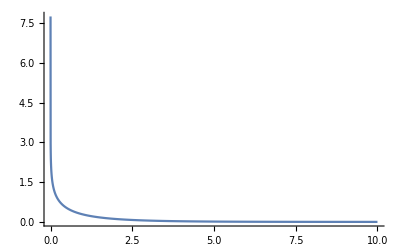

```mathematica
p[k]=1/(2*c*s)*NIntegrate[Exp[-k/(2*c*s*U)]/U,{U,0,1}];
Plot[p[k]/.{c->0.01,s->100},{k,0,10},PlotRange->All]
```

NIntegrate::inumr: The integrand ⅇ^(-k/(2 c s U))/U has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

NIntegrate::inumr: The integrand ⅇ^(-0.000102143/(c s U))/U has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

-Graphics-

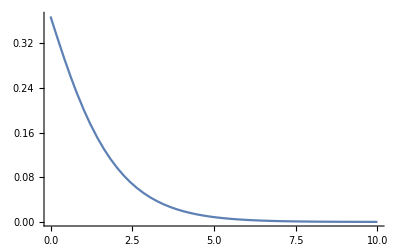

```mathematica
Pprey[k]=1/(2*c*s)*NIntegrate[Exp[-k/(2*c*s*U)]/U,{U,0,1}];
Ppred[m] = 1/(2*c*s)*Gamma[2*c*s,m+1];
Plot[Pprey[k]/.{c->0.01,s->100},{k,0,10},PlotRange->All]
Plot[Ppred[m]/.{c->0.01,s->100},{m,0,10},PlotRange->All]
```

Expected values

```mathematica
Integrate[k*1/(2*c*s)*Integrate[Exp[-k/(2*c*s*U)]/U,{U,0,1}],{k,0,Infinity}]
```

∫_0^∞ ConditionalExpression[(k Gamma[0,k/(2 c s)])/(2 c s),Re[k/(c s)]≥0]ⅆk

```mathematica
Sum[k*1/(2*c*s)*NIntegrate[Exp[-k/(2*c*s*U)]/U,{U,0,1}]/.{c->0.001,s->10},{k,0,100}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in U near {U} = {1.63073×10^-29}. NIntegrate obtained 757.365 and 296.932 for the integral and error estimates.

NIntegrate::inumr: The integrand ⅇ^(-1/(2 c s U))/U has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

NIntegrate::inumr: The integrand ⅇ^(-1/(c s U))/U has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

General::munfl: (1.40652×10^-307)/10 is too small to represent as a normalized machine number; precision may be lost.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

1.89163×10^-22

```mathematica
ListContourPlot[ParallelTable[{k,Sum[k*1/(2*c*s)*NIntegrate[Exp[-k/(2*c*s*U)]/U,{U,0,1}],{k,0,100}]},{s,10,100,10},{c,0.01,0.1,0.01}]]
```

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 9
                                                     -29
     recursive bisections in U near {U} = {1.63073 10   }
    . NIntegrate obtained 757.365 and 296.932
     for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb
     will be suppressed during this calculation.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 9
                                                     -29
     recursive bisections in U near {U} = {1.63073 10   }
    . NIntegrate obtained 757.365 and 296.932
     for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb
     will be suppressed during this calculation.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 9
                                                     -29
     recursive bisections in U near {U} = {1.63073 10   }
    . NIntegrate obtained 757.365 and 296.932
     for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb
     will be suppressed during this calculation.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 9
                                                     -29
     recursive bisections in U near {U} = {1.63073 10   }
    . NIntegrate obtained 757.365 and 296.932
     for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb
     will be suppressed during this calculation.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 9
                                                     -29
     recursive bisections in U near {U} = {1.63073 10   }
    . NIntegrate obtained 757.365 and 296.932
     for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb
     will be suppressed during this calculation.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 9
                                                     -29
     recursive bisections in U near {U} = {1.63073 10   }
    . NIntegrate obtained 757.365 and 296.932
     for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb
     will be suppressed during this calculation.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 9
                                                     -29
     recursive bisections in U near {U} = {1.63073 10   }
    . NIntegrate obtained 757.365 and 296.932
     for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb
     will be suppressed during this calculation.

-Graphics-